```mathematica
Needs["dsvsolve`"];
```

## Input

Edit or simply evaluate the following cell to see the input

{$$domains→{{-L,-L,0,L},{0,-L,L,0}},$$coefficients→{1,1},$$traction→0,$$wheretraction→{0,0},$$bending→{-M/(√2),-M/(√2)}}

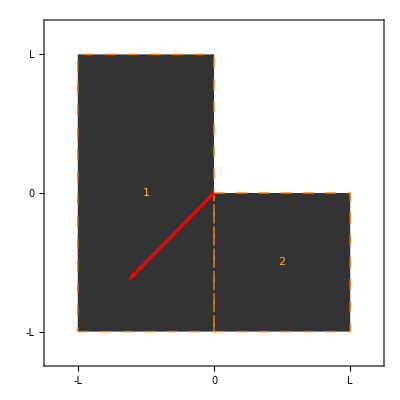

```mathematica
example={$$domains->{{-L, -L, 0, L}, {0, -L, L, 0}},
$$coefficients->{1, 1},
$$traction->0,$$wheretraction->{0, 0},
$$bending->    {-M/Sqrt[2],-M/Sqrt[2]}}
dSVcShowInput[example]
```

## Output

Evaluate the following cell to solve the problem and see the output

```mathematica
sol = {AB, rG, JB, sigma, gobj, details} = dSVcSolve[example];
gsol=dSVcShowOutput[example, sol]
```

First::nofirst: {} has zero length and no first element.

Last::nolast: {} has zero length and no last element.

123456

Evaluate the following cell to print the above output

```mathematica
CellPrint/@Rest/@Last[sol];
Print/@Cases[gsol,Graphics[___],Infinity];
```

Numerical assumptions for visualization purposes

{L→0.75,M→0.94}

Areas of elementary domains Ai

{{2 L^2,L^2}}

Total Area A

3 L^2

Static moments of elementary domains sPi

{{{-L^3,0},{L^3/2,-L^3/2}}}

Total static moment sP

{{-L^3/2,-L^3/2}}

Centroids of elementary domains Gi

{{{-L/2,0},{L/2,-L/2}}}

Centroid G

{{-L/6,-L/6}}

Euler inertia tensors of elementary domains IPi

{{{{(2 L^4)/3,0},{0,(2 L^4)/3}},{{L^4/3,-L^4/4},{-L^4/4,L^4/3}}}}

Total Euler inertia tensor IP

{{L^4,-L^4/4},{-L^4/4,L^4}}

Inertia tensor after translation in the centroid IG

{{(11 L^4)/12,-L^4/3},{-L^4/3,(11 L^4)/12}}

Principal inertia momoments (jI, jII) and associated directions

{{(7 L^4)/12,{-1,1}},{(5 L^4)/4,{1,1}}}

Rotation to principal directions

45.

Radii of gyration (ρI, ρII)

{{(√7 L)/6,1/2 √(5/3) L}}

Section moduli (WI, WII) and associated directions

{{{(7 L^3)/20,(7 L^3)/16},{-1,1}},{{(5 L^3)/8,(5 L^3)/8},{1,1}}}

Coefficients {a0,a1,a2} for sigma (= a0 + a1 x1 + a2 x2)

{0,(2 √2 M)/(5 L^4),-(2 √2 M)/(5 L^4)}

Sigma in principal axis (ξ,η)

(-0.8 "η" M+0.133333 L M)/L^4

Neutral axis

{x2→x1}

Intersections of neutral axis with principal axis

{Last[{}],Last[{}]}

Inertia ellipse equation

5 L^2==11 x1^2+8 x1 x2+11 x2^2+5 L (x1+x2)

Sigma values in relevant points

{{{0,0},0},{{-L,-L},0},{{-L,L},-(4 √2 M)/(5 L^3)},{{0,L},-(2 √2 M)/(5 L^3)},{{0,-L},(2 √2 M)/(5 L^3)},{{L,0},(2 √2 M)/(5 L^3)},{{L,-L},(4 √2 M)/(5 L^3)}}

Kern (convex hull has been computed on a numerical instance!)

{{-(3 L)/7,-L/14},{-(5 L)/16,-(5 L)/16},{-L/14,-(3 L)/7},{L/5,-(3 L)/10},{-(3 L)/10,L/5},{-(3 L)/10,L/5}}

-Graphics-

-Graphics-

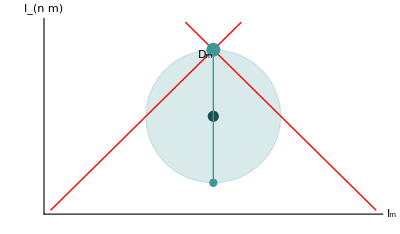

-Graphics-